# § Shape Deformation: Analysis Code

Nicholas E. Brunk - nbrunk@wolfram.com - nbrunk90@gmail.com - 2020.12.21

## § Basic Initialization

```mathematica
(* The following loads dependent functions written over the course of multiple projects (the majority are not used directly): *)
Get@FileNameJoin[{NotebookDirectory[],"NBTools.wl"}]
```

## § Thermodynamic & Geometric Plots

Energy_nanomembrane columns sequentially specify:  	{Local KE, Local PE, Local Net, Total Net, Bath KE, Bath PE}	→	{locKin, locPot, locNet, totNet, bathKin, bathPot}			(code names assigned below)

Energy_in_parts columns sequentially specify the:  		Local {KE, BE, SE, TE, LJ-E, ES-E, VT-E}					→	{kinetic, bending, stretching, tension, lennard, electrostatic,volTension}	(code names assigned below)

```mathematica
ClearAll@gatherSeries;ClearAll@simPlot;ClearAll@setPlot;
```

Preliminary Data Gathering

```mathematica
(* A function to gather and format all series data in a set of simulation directories and - if enabled with "y" - append each to a corresponding dataset for multiple simulations: *)
gatherSeries[directories_:{"outfiles"},set_:"n"]:=
Module[{},If[Length@directories>1,
ClearAll@setArea;ClearAll@setVolume;ClearAll@setTemp;ClearAll@setEnergy;ClearAll@setEnergyParts;ClearAll@setFinArea;ClearAll@goodDirs;ClearAll@badDirs;ClearAll@preAnnealDriftBadDirs;ClearAll@postAnnealDriftBadDirs;
ClearAll@extremeDivergenceBadDirs;
ClearAll@legends;ClearAll@minutesRan;];
 (* Clear the set once, then do single-simulation gather for each simulation in the list, assembling the set of series, if requested: *)
Module[{oldDirectory=Directory[](*,simParamOut*)},

If[Directory[]≠#,SetDirectory[#]];
simParamOut=Import["simulation.out","Table"];

(* Input parameters relevant to the run: *)
	(* Real Parameters: *)
vertCount=Last@Flatten@simParamOut⟦Sequence@@Position[simParamOut,{"Number","of","vertices:",___}]⟧;
sphRadius=Last@Flatten@simParamOut⟦Flatten@Position[simParamOut,{"Unit","radius",___}]⟧;
qStr=Last@Flatten@simParamOut⟦Sequence@@Position[simParamOut,{"Total","charge",___}]⟧;
αOcc=Last@Flatten@simParamOut⟦Sequence@@Position[simParamOut,{"Fractional",___}]⟧;
cS=Last@Flatten@simParamOut⟦Sequence@@Position[simParamOut,{"Salt",___}]⟧;
κb=Last@Flatten@simParamOut⟦Sequence@@Position[simParamOut,{"Bending","rigidity:",___}]⟧;
κs=Last@Flatten@simParamOut⟦Sequence@@Position[simParamOut,{"Stretching","constant:",___}]⟧;
σA=Last@Flatten@simParamOut⟦Sequence@@Position[simParamOut,{"Surface","Tension",___}]⟧;
σV=Last@Flatten@simParamOut⟦Sequence@@Position[simParamOut,{"Volume","Tension",___}]⟧;
geomConstraint=Last@Flatten@simParamOut⟦Sequence@@Position[simParamOut,{"Rigid","geometric","constraint:",___}]⟧;
randomFlag=Last@Flatten@simParamOut⟦Sequence@@Position[simParamOut,{"Randomness",___}]⟧;
tempInit=Last@Flatten@simParamOut⟦Sequence@@Position[simParamOut,{"Initial","Temperature",___}]⟧;
ΔtStep=Sequence@@Flatten@simParamOut⟦Sequence@@Position[simParamOut,{"Timestep","(dt):",___}],3⟧;
targetTtot=Last@Flatten@simParamOut⟦Sequence@@Position[simParamOut,{"Timestep","(dt):",___}]⟧;
	(* Conservation Parameters: *)
offFlagh=Last@Flatten@simParamOut⟦Sequence@@Position[simParamOut,{"Off-file loaded:",___}]⟧;
chainLength=N@Last@Flatten@simParamOut⟦Sequence@@Position[simParamOut,{"Number","of","thermostats",___}]⟧;
tMassQ=Last@Flatten@simParamOut⟦Sequence@@Position[simParamOut,{"Thermostat","mass","(Q):",___}]⟧;
annealFlagh=Last@Flatten@simParamOut⟦Sequence@@Position[simParamOut,{"Annealing:",___}]⟧;
annealFreqh=Last@Flatten@simParamOut⟦Sequence@@Position[simParamOut,{"Anneal","frequency:",___}]⟧;
annealDurationh=Last@Flatten@simParamOut⟦Sequence@@Position[simParamOut,{"Anneal","duration:",___}]⟧;
tAnnealFac=N@Last@Flatten@simParamOut⟦Sequence@@Position[simParamOut,{"Temperature","annealing","decrement:",___}]⟧;
qAnnealFac=N@Last@Flatten@simParamOut⟦Sequence@@Position[simParamOut,{"Thermostat","mass","decrement:",___}]⟧;

(* Redefine the frequency of annealing, set to infinity if it never anneals: *)
If[(annealFlagh=="n"||chainLength==1),annealFreqh=∞];

(* Import time-series quantities of interest: *)
area=Import["area.dat","Table","FieldsSeparators"->" "];
volume=Import["volume.dat","Table","FieldsSeparators"->" "];
temp=Import["temperature.dat","Table","FieldsSeparators"->" "];
momentum=Import["total_momentum.dat","Table","FieldsSeparators"->" "];
energy=Transpose@Import["energy_nanomembrane.dat","Table","FieldsSeparators"->" "];
energy=Table[Transpose[{energy⟦1⟧,energy⟦i⟧}],{i,2,Length@energy,1}];
energyParts=Transpose@Import["energy_in_parts_kE_bE_sE_tE_ljE_esE.dat","Table","FieldsSeparators"->" "];
energyParts=Table[Transpose[{energyParts⟦1⟧,energyParts⟦i⟧}],{i,2,Length@energyParts,1}];
	{kinetic,bending,stretching,tension,lennard,electrostatic,volTension}=energyParts;

(* Remove any cases of "nan" errors from the time-series of interest, define relevant pieces component-wise: *)
{area,volume,temp,momentum}=DeleteCases[#,{x_,y_}/;Head[y]==String]&/@{area,volume,temp,momentum};
energy=DeleteCases[#,{x_,y_}/;Head[y]==String]&/@energy;
	{locKin,locPot,locNet,totNet,bathKin,bathPot}=energy;
energyParts=DeleteCases[#,{x_,y_}/;Head[y]==String]&/@energyParts;
	{kinetic,bending,stretching,tension,lennard,electrostatic,volTension}=energyParts;

(* Define some useful quantities about the simulation: *)
annealGridLines=(annealFreqh*Range[10])/.x_Integer:>{x,Dotted};
	If[MemberQ[Flatten[Map[Head,annealGridLines,{2}]],DirectedInfinity],annealGridLines={}];
actualTSteptot=First@Last@area;
finSys=Last/@Last/@{area,volume,temp,momentum};
initEnergy=Last/@First/@energyParts;
finEnergy=Last/@Last/@energyParts⟦1;;4⟧;
If[FileExistsQ["area.dat"],minutesRan=QuantityMagnitude[UnitConvert[FileDate["area.dat"]-FileDate["simulation.out"],"Minutes"]],minutesRan=0];

(* Begin the aggregation of a set of simulation data: *)
If[Head[setArea]==Symbol,setArea={}];AppendTo[setArea,area];
If[Head[setVolume]==Symbol,setVolume={}];AppendTo[setVolume,volume];
If[Head[setTemp]==Symbol,setTemp={}];AppendTo[setTemp,temp];
If[Head[setEnergy]==Symbol,setEnergy={}];AppendTo[setEnergy,energy];
If[Head[setEnergyParts]==Symbol,setEnergyParts={}];AppendTo[setEnergyParts,energyParts];
If[Head[legends]==Symbol,legends={}];AppendTo[legends,StringDelete[#,{"Titrating_ks_","outfiles"}]];

(* If requested, append relevant per-simulation series to the set (only if the above issues did not arise): *)
Module[{qualityConditions={
(* Check for moderate pre-annealing drift (δ > 1%: *)
Last[First@totNet]≈Last[Last@Cases[totNet,{x_,y_}/;x<annealFreqh]],
(* Check for moderate post-annealing drift (δ > 1%): *)
(1.025Last[First@totNet])≥Last[Last@totNet],
(* Check for severe drift (δ > 5%). *)
First@Last@area≥(0.75*targetTtot)}},
If[(set=="y")&&AllTrue[qualityConditions,(#==True)&],If[Head[goodDirs]==Symbol,goodDirs={}];AppendTo[goodDirs,#];,If[Head[badDirs]==Symbol,badDirs={}];AppendTo[badDirs,#]];
(* Categorize the 'badDirs,' which failed for which reason: *)
If[Head[preAnnealDriftBadDirs]==Symbol,preAnnealDriftBadDirs={}];
If[Head[postAnnealDriftBadDirs]==Symbol,postAnnealDriftBadDirs={}];
If[Head[extremeDivergenceBadDirs]==Symbol,extremeDivergenceBadDirs={}];
Which[
TrueQ[qualityConditions⟦1⟧==False],AppendTo[preAnnealDriftBadDirs,#],
TrueQ[qualityConditions⟦2⟧==False],AppendTo[postAnnealDriftBadDirs,#],
TrueQ[qualityConditions⟦3⟧==False],AppendTo[extremeDivergenceBadDirs,#]];
SetDirectory[oldDirectory];]]&/@directories;

(* If requested, organize the set QoI's conveniently by name and assign the end-state: *)
If[set=="y"(*&&AllTrue[{setEnergyParts,setEnergy,legends},(Head[#]≠Symbol)&]*),
(* Segregate by series QoI's (still a list of each simulations' entire time-series for the given quantity): *)
{setKinetic,setBending,setStretching,setTension,setLJ,setES,setVolTension}=(setEnergyParts⟦All,#⟧&/@Range[7]);
setLocalNet=setEnergy⟦All,3⟧;setTotalNet=setEnergy⟦All,4⟧;
(* Assign the end QoIs for the set: *)
{setFinArea,setFinVolume,setFinKinetic,setFinBending,setFinStretching,setFinTension,setFinLJ,setFinES,setFinVolTension,setFinLocalNet,setFinTotalNet}=(endYAvg/@#)&/@{setArea,setVolume,setKinetic,setBending,setStretching,setTension,setLJ,setES,setVolTension,setLocalNet,setTotalNet};
(* Assign the initial QoIs for the set: *)
{setInitArea,setInitVolume,setInitKinetic,setInitBending,setInitStretching,setInitTension,setInitLJ,setInitES,setInitVolTension,setInitLocalNet,setInitTotalNet}=(Last/@First/@#)&/@{setArea,setVolume,setKinetic,setBending,setStretching,setTension,setLJ,setES,setVolTension,setLocalNet,setTotalNet};
(* Assign the delta QoIs for the set: *)
{setDeltaArea,setDeltaVolume,setDeltaKinetic,setDeltaBending,setDeltaStretching,setDeltaTension,setDeltaLJ,setDeltaES,setDeltaVolTension,setDeltaLocalNet,setDeltaTotalNet}={setFinArea,setFinVolume,setFinKinetic,setFinBending,setFinStretching,setFinTension,setFinLJ,setFinES,setFinVolTension,setFinLocalNet,setFinTotalNet}-{setInitArea,setInitVolume,setInitKinetic,setInitBending,setInitStretching,setInitTension,setInitLJ,setInitES,setInitVolTension,setInitLocalNet,setInitTotalNet};
setAreaRatio=setFinArea/setInitArea;]];

(* A function to clear the definitions of all aggregate, multiple-simulation datasets (called prior to the plotting of a new set of simulations via setPlot[~]): *)
clrSet:=Module[{},ClearAll@setArea;ClearAll@setVolume;ClearAll@setTemp;ClearAll@setEnergy;ClearAll@setEnergyParts;ClearAll@setFinArea;ClearAll@goodDirs;ClearAll@legends;]

(* A general function to add a legend tooltip upon mouseover to each dataset (uses 'legends' defined in gatherData[~] by default, can use Block[{legends = ...}, ~] for others):  *)
toolTipData[data_]:=Table[Tooltip[data⟦i⟧,legends⟦i⟧],{i,1,Length@legends}]

(* A function to provide information on initial and final quantities and the temporal variation (rounds to a percent of the original value): *)
temporal[dataSeries_List]:=NumberForm[#,4]&/@(If[#≠0,Round[#,#/100],#]&/@
{Last@First[#],Last@Last[#],If[First[Last/@#]≠0,Last[Last/@#]/First[Last/@#],∞],Mean@weightedDiffData@dataSeries,If[First[Last/@#]≠0,(Mean@weightedDiffData@dataSeries)/First[Last/@#],∞],If[Mean[Last/@#]≠0,(StandardDeviation[#]/Mean[#])&@weightedDiffData[dataSeries],∞]}&@dataSeries)

(* A function to compute the final QoI (e.g. setFinES) and keep track of which simulation it corresponded to {q, Subscript[c, s], σ, Subscript[κ, b], Subscript[κ, s], Subscript[QoI, ∞]}: *)
aggSetData[finalQoI_]:=Flatten/@Transpose[{N@ToExpression/@StringCases[legends,NumberString],finalQoI}];
```

Individual Simulation Analysis

```mathematica
(* Plot all series information for a single simulation directory: *)
simPlot[directory_String:"outfiles"]:=
Module[{absDir=AbsoluteFileName@directory,globalOpts={Joined->True,PlotRange->{All,{Automatic,All}}},
energiesPlot,lowEnergiesPlot,electrostaticsPlot,tempPlot,geomPlot,areaPlot,volumePlot,globalPlot,selectGlobalPlot,paramTable},
(* Gather the series data to be analysed: *)
gatherSeries[{directory}];

(* Thermodynamics: *)
energiesPlot=Block[{legends={"Kinetic","Bending","Stretching","Tension","Lennard-Jones","Electrostatic","Volume Tension"}},
ListPlot[toolTipData@energyParts,PlotRange->All,PlotLabel->myStyle@"Membrane Energies",PlotStyle->{{Thick,Dashed},Thick,Thick,Thick,Thick,Thick},GridLines->{annealGridLines,None},globalOpts]];
lowEnergiesPlot=
Block[{legends={"Kinetic","Bending","Stretching","Lennard-Jones"}},
ListPlot[toolTipData@{kinetic,bending,stretching,lennard},PlotRange->All,PlotStyle->Table[{Thick,ColorData[1,i]},{i,{1,2,3,5}}],
GridLines->{annealGridLines,{{2 π κb,Dotted}}~Join~Table[{Mean[weightedDiffData@energyParts⟦i⟧],{Dashed,ColorData[1,i]}},{i,{1,2,3,5}}]},PlotLabel->myStyle@"Kinetic, Bend, Stretch, LJ Energies",globalOpts]];
electrostaticsPlot=Block[{legends={"Surface Tension","Electrostatic","Volume Tension"}},
ListPlot[toolTipData@{tension,electrostatic,volTension},PlotRange->All,PlotLabel->myStyle@"Electrostatic, Tension Energies",PlotStyle->Table[{Thick,ColorData[1,i]},{i,{4,6,7}}],GridLines->{annealGridLines,Table[{Mean[weightedDiffData@energyParts⟦i⟧],{Dashed,ColorData[1,i]}},{i,{4,6,7}}]},globalOpts]];
globalPlot=
Block[{legends={"Local Kinetic","Local Potential","Local Net","Total Energy","Bath Kinetic","Bath Potential"}},
ListPlot[toolTipData@energy,PlotLabel->myStyle@"Global Energies",PlotStyle->Directive[Thick],GridLines->{annealGridLines,None},globalOpts]];
selectGlobalPlot=
Block[{legends={"Total Energy","Local Potential"}},
ListPlot[toolTipData[{totNet,locPot}],PlotRange->All,PlotLabel->myStyle@"Total & Membrane Potential Energy",PlotStyle->{{Thick,ColorData[1,4]},{Thick,ColorData[1,2]}},GridLines->{annealGridLines,Last/@{First@#,Last@#}&@totNet~Join~{1.05(Last@First@totNet)}},globalOpts]];
tempPlot=ListPlot[temp,PlotLabel->myStyle@"Temperature",PlotStyle->Thick,PlotRange->All,GridLines->{annealGridLines,{{Last@First@temp,Dotted},1.0,{Mean[weightedDiffData@temp],{Dashed,ColorData[1,1]}}}},globalOpts];
(* Geometrics: *)
areaPlot=Block[{legends={"Area"}},ListPlot[toolTipData@{area},PlotRange->All,GridLines->{annealGridLines,{{Last@First@area,Dotted},4π,{Mean[weightedDiffData@area],{Dashed,ColorData[1,1]}}}},PlotStyle->Thick,PlotLabel->myStyle@"Membrane Area",globalOpts]];
volumePlot=Block[{legends={"Volume"}},ListPlot[toolTipData@{volume},GridLines->{annealGridLines,{{Last@First@volume,Dotted},4/3 π,{Mean[weightedDiffData@volume],{Dashed,ColorData[1,1]}}}},PlotStyle->Thick,PlotLabel->myStyle@"Membrane Volume",globalOpts]];
(* Information tables: *)
consParamTable=TableForm[N[{If[chainLength==1.,"1 (NVE)",chainLength],tempInit,tMassQ,annealFlagh,annealFreqh,annealDurationh,tAnnealFac,qAnnealFac,offFlagh,randomFlag}]/.{x_Real:>{myStyle@x},x_String:>{myStyle@x}},
TableHeadings->{myStyle/@{"C_L","T_0^tg","Q","Anneal","a_freq","a_dur","f_T^ann","f_Q^ann","Off-loaded","Random"},myStyle/@{"Thermostat"}},TableAlignments->Center];
paramTable=TableForm[N[{vertCount,sphRadius,qStr,αOcc,cS,σA,σV,κb,κs,geomConstraint,ΔtStep,actualTSteptot,minutesRan,actualTSteptot/minutesRan}]/.{x_Real:>{myStyle@x},x_String:>{myStyle@x}},
TableHeadings->{myStyle/@{"N_v","r","q_str","α","c_s","σ_A","σ_V","κ_b","κ_s","G_con","Δt", "t_tot","t_run","r_run"},myStyle/@{"System"}},TableAlignments->Center];
temporalTable=Labeled[
TableForm[(myStyle/@temporal@#)&/@({area,volume,temp,totNet,locPot}~Join~energyParts),
TableHeadings->{myStyle/@{"Area","Volume","Temperature","Total Energy","Local Potential","Kinetic","Bending","Stretching","Surface Tension","LJ-E","ES-E","Volume Tension"},myStyle/@{"Initial","Final","Drift (Final/Initial)","Mean","Mean Drift (Mean/Initial)","Coeff. Variation"}},TableAlignments->Center],myStyle@"Temporal Information",Top];

Column[{Labeled[
GraphicsGrid[{{energiesPlot,lowEnergiesPlot,electrostaticsPlot,areaPlot},{globalPlot,selectGlobalPlot,tempPlot,volumePlot}},ImageSize->Full,PlotLabel->Style[StringDelete[directory,{"E:\\Box Sync\\Research Code\\Shapes Simulations\\Shapes_Simulations_Code\\2017.08.29_Area\\cmake-build-debug\\outfiles","E:\\Box Sync\\Research Data\\Shape_Deformation\\Surface_Tension\\Bulk_Runs\\","outfiles"}],22]],myStyle@"Temporal Evolution Plots",Top],Spacer[3],Row@{consParamTable,Spacer[75]paramTable,Spacer[75],temporalTable},Spacer[3],
Button[myStyle@"Click for simulation movie in Ovito.",SystemOpen[FileNameJoin[{absDir,"p.lammpstrj"}]],ImageSize->500],Spacer[3],
Row@{Button[myStyle@"Click to open directory.",SystemOpen[absDir],ImageSize->300],Spacer[30],Button[myStyle@"Click to copy directory path.",CopyToClipboard[absDir],ImageSize->300]}},Center]]
```

Bulk Simulation Analysis

```mathematica
(* Aggregate and plot the information from an entire set of simulations within a given directory: *)
setPlot[directories_List,temporalTables_:"n"]:=
Module[{globalOpts={PlotRange->{All,All},PlotStyle->Thick,Frame->True}},
(* Gather the requested set of time-series: *)
gatherSeries[directories,"y"];
(* Define the plots: *)
setTempPlot=ListLinePlot[toolTipData@setTemp,PlotLabel->myStyle@"Temperature",globalOpts];
setBendingPlot=ListLinePlot[toolTipData@setBending,PlotLabel->myStyle@"Bending Energies",globalOpts];
setElectrostaticsPlot=ListLinePlot[toolTipData@setES,PlotLabel->myStyle@"Electrostatic Energies",globalOpts];
setAreaPlot=ListLinePlot[toolTipData@setArea,PlotLabel->myStyle@"Area",globalOpts];
setTotalNetPlot=ListLinePlot[toolTipData@setTotalNet,PlotLabel->myStyle@"Global Net Energy",globalOpts];
setStretchingPlot=ListLinePlot[toolTipData@setStretching,PlotLabel->myStyle@"Stretching Energies",globalOpts];
setTensionPlot=ListLinePlot[Flatten[{toolTipData@setTension,toolTipData@setVolTension},1],PlotLabel->myStyle@"Tension Energies",globalOpts];
setVolumePlot=ListLinePlot[toolTipData@setVolume,PlotLabel->myStyle@"Volume",globalOpts];

(* The set of time-series and aggregate endpoint plots: *)
Column@{GraphicsGrid[{
(* Geometric Dependency plots (elastic dependency commented out below): *)
{Module[{segData,trimmedData},
segData=Sort@GatherBy[aggSetData[setAreaRatio],#⟦8⟧&];
trimmedData=Map[{#⟦7⟧,Last@#}&,segData,{2}];
ListLinePlot[trimmedData,PlotLabel->myStyle@"Area Ratio(c_s)",PlotStyle->{{Red,Thick},{Orange,Thick},{Yellow,Thick},{Green,Thick},{Blue,Thick},{Purple,Thick},{Black,Thick}},(*,PlotLegends->myStyle/@Flatten[DeleteDuplicates/@Map[#⟦8⟧&,segData,{2}]]*)globalOpts]],
Module[{},
segData=Sort@GatherBy[aggSetData[setFinES],#⟦8⟧&];
trimmedData=Map[{#⟦7⟧,Last@#}&,segData,{2}];
ListLinePlot[trimmedData,PlotLabel->myStyle@"Electrostatic ΔES(c_s)",PlotStyle->{{Red,Thick},{Orange,Thick},{Yellow,Thick},{Green,Thick},{Blue,Thick},{Purple,Thick},{Black,Thick}},globalOpts]],
Module[{segData,trimmedData},
segData=Sort@GatherBy[aggSetData[setAreaRatio],#⟦7⟧&];
trimmedData=Map[{#⟦8⟧,Last@#}&,segData,{2}];
ListLinePlot[trimmedData,PlotLabel->myStyle@"Area Ratio(σ_A)",PlotStyle->{{Red,Thick},{Orange,Thick},{Yellow,Thick},{Green,Thick},{Blue,Thick},{Purple,Thick},{Black,Thick}},globalOpts]],
Module[{},
segData=Sort@GatherBy[aggSetData[setFinES],#⟦7⟧&];
trimmedData=Map[{#⟦8⟧,Last@#}&,segData,{2}];
ListLinePlot[trimmedData,PlotLabel->myStyle@"Electrostatic ΔES(σ_A)",PlotStyle->{{Red,Thick},{Orange,Thick},{Yellow,Thick},{Green,Thick},{Blue,Thick},{Purple,Thick},{Black,Thick}},globalOpts]]},
(* Thermodynamic Series plots: *)
{setTempPlot,setBendingPlot,setElectrostaticsPlot,setAreaPlot},
{setTotalNetPlot,setStretchingPlot,setTensionPlot,setVolumePlot}
(* Elastic depdence plots {ΔA(Subscript[κ, s],Subscript[κ, b]), ΔES(Subscript[κ, s],Subscript[κ, b]), ΔA(Subscript[n, FvK]), ΔES(Subscript[n, FvK])} *)
(*{ListPlot3D[(#⟦{4,5,-1}⟧)&/@aggSetData[setFinArea],PlotLabel->myStyle@"Area ΔA_∞(κ_b,κ_s)",AxesLabel->myStyle/@{"κ_b","κ_s","A_∞"},Mesh->All,PlotRange->All,TicksStyle->Directive["Label",14,Black,FontFamily->"Times New Roman"]],
ListPlot3D[(#⟦{4,5,-1}⟧)&/@aggSetData[setFinES-setInitES],PlotLabel->myStyle@"Electrostatic ΔES_∞(κ_b,κ_s)",AxesLabel->myStyle/@{"κ_b","κ_s","ΔES_∞"},Mesh->All,PlotRange->All,TicksStyle->Directive["Label",14,Black,FontFamily->"Times New Roman"]],
ListLinePlot[toolTipData@(((#⟦{4,5,-1}⟧)&/@aggSetData[setFinArea])/.{κbh_Integer,κsh_Integer,QoI_}:>{κsh/κbh,QoI}),PlotLabel->myStyle@"Area ΔA_∞(n_FvK)",Mesh->All,PlotRange->All],
ListLinePlot[toolTipData@(((#⟦{4,5,-1}⟧)&/@aggSetData[setFinES-setInitES])/.{κbh_Integer,κsh_Integer,QoI_}:>{κsh/κbh,QoI}),PlotLabel->myStyle@"Electrostatic ΔES_∞(n_FvK)",Mesh->All,PlotRange->All]}*)},PlotLabel->myStyle@"Series Plots",ImageSize->Full],
Spacer[100],
If[temporalTables=="y",
(* Produce a table of the initial and final (non-relative) contributions each component of the energy made: *)
Labeled[Multicolumn[Table[
Labeled[
Framed@TableForm[(myStyle/@Last/@{First[#],Last[#],Last[#]-First[#],(Last[#]-First[#])/First[#]}&/@setEnergyParts⟦i⟧)~Join~{(myStyle/@Last/@{First[#],Last[#],Last[#]-First[#],(Last[#]-First[#])/First[#]}&@setTotalNet⟦i⟧)},TableHeadings->{myStyle/@{"KE","BE","SE","TE","LJ","ES", "Net"},myStyle/@{"Initial E_i_0","Final E_i'","Absolute ΔE_i","Relative ΔE_i/E_i_0"}},TableAlignments->Center]//Quiet,
Style[legends⟦i⟧,22,FontFamily->"Times New Roman",Underlined,Bold,Italic],Top],{i,1,Length@legends}],Spacings->5],
Style["Duration Energy Information",26,FontFamily->"Times New Roman",Underlined,Bold,Italic],Top],Null]}]
```

## § Simulation Visualization, Energetics Profiling

Preliminary Mesh Loading

You will need to point this to the directory containing the discretization files (within the Import line defining geomData).

```mathematica
(* Function to load a given mesh discretization (mesh must be loaded prior to : *)
loadMesh[D_]:=Module[{},
(* Importing the geometric data: *)
geomData=Import["E:\\Box Sync\\Research Code\\Shapes Simulations\\Shapes_Simulations_Code\\Shapes_Simulation\\cmake-build-debug\\infiles\\3_"<>ToString[D]<>".dat","Table"];
(* Defining the coordinates of the vertices [(3,4) = 372 ; (3,8) = 972]: *)
vertCoords=geomData⟦5;;Last[geomData⟦1⟧]-1+5,2;;4⟧;
	(* The number of vertices: *)
	numVerts=Length@vertCoords;
(* Defining the faces by which vertices they consist of, using the number of triangular faces and the line at which they begin being specified: *)
faceVerts=With[{nTri=Last@Flatten@geomData⟦Sequence@@Position[geomData,{"#","Number","of","Triangles=",___}]⟧,lineTri=Position[geomData,"triangles"]⟦1,1⟧},
geomData⟦lineTri+2;;lineTri+nTri+1,2;;4⟧];
(* Defining the faces by their coordinates directly, as well: *)
faceCoords=faceVerts/.{x_,y_,z_}:>{vertCoords⟦1+x⟧,vertCoords⟦1+y⟧,vertCoords⟦1+z⟧};
(* Assess the areas of the each face [memory leak bug]: *)
(*faceArea=Area[Triangle[#]]&/@faceCoords;*)
(* Compute the dual lattice vertices (face center coordinates): *)
dualCoords=Mean/@(faceVerts/.{x_,y_,z_}:>{vertCoords⟦1+x⟧,vertCoords⟦1+y⟧,vertCoords⟦1+z⟧});
(* Defining the net initial mesh / membrane: *)
netMesh=RepairMesh@MeshRegion[vertCoords,Triangle[#]&/@{1+faceVerts},PlotTheme->"SmoothShading"];
(* Extract the length of the edges: *)
edgeLengths=MeshCells[netMesh,1]/.{v1_,v2_}:>{vertCoords⟦v1⟧,vertCoords⟦v2⟧}/.{v1_,v2_}:>(v1-v2)/.Line:>Norm;]
```

Preliminary Data Gathering

Dump file format details:	Starts at a timestep (0) and dumps every (moviefreq=100) steps.  [*.off files are written every 10000 steps and POVRay files are written every 100000, if enabled.]

Standard off file details:		Produced every 10K steps, contains sequentially rows and sections specifying:  {{N_V,N_F,N_E}, {vCoords alone}, {3, face vertices, r, g, b, a}}

Energy off file details:		Produced at the end of the run, contains sequentially rows and sections specifying:  {{N_V,N_F,N_E}, {vCoords alone}, {3, face vertices, r, g, b, a}}  where {r = 0, g=ΔF_ES_i/ΔF_ES_max=(F_ES_i - F_ES_min)/(F_ES_max - F_ES_min) , b=1-g , a = 1}	(colors to be used in automatic software).

```mathematica
(* Defines a function to import coordinates, assess vertex charge, etc: *)
assignShapeDetails[directory_String:"outfiles",dumpStep_:"end"]:=
Block[{oldDir=Directory[],stream,numAtoms,area},

(* Simply assess the final timestep: *)
If[Directory[]≠directory,SetDirectory[directory]];
area=Import["area.dat","Table","FieldsSeparators"->" "];
actualTSteptot=First@Last@area;

(* Load the mesh file for this simulation: *)
(*loadMesh[Round@Abs[simParams[directory]⟦3⟧]];*)

(* Closes any pre-existing stream (if open, else squelching the error) and re-initiates the stream: *)
Close@stream//Quiet;
stream=OpenRead["p.lammpstrj"];
(* Locate dump step (Subscript[t, d]) and extract the number of atoms: *)
Do[Find[stream,{"ITEM: TIMESTEP"}],If[dumpStep=="end",actualTSteptot/1000-3,dumpStep]+1];
(* Extract the number of atoms: *)
Find[stream,{"ITEM: NUMBER OF ATOMS"}];
numAtoms=Read@stream;
(* Finds the line before which the n^th time step's data begins: *)
Find[stream,{"ITEM: ATOMS index type x y z "}];
(* Stream in only the relevant dump step's coordinates (for all atoms): *)
data=ToExpression[#,InputForm]&/@StringSplit/@ReadList[stream,"String",numAtoms];
(* Define all coordinates together, the mesh coordinates alone, and ion coordinates alone: *)
coords=#⟦3;;5⟧&/@data;
meshCoords=#⟦3;;5⟧&/@Cases[data,entry_/;((entry⟦2⟧==1)||(entry⟦2⟧==-1))];
ionCoords=#⟦3;;5⟧&/@Cases[data,entry_/;(entry⟦2⟧==2)];
radius=1(*(simParams[directory]⟦1⟧)*);
coords=radius*coords;meshCoords=radius*meshCoords;ionCoords=radius*ionCoords;
vertAreas=#⟦-2⟧&/@data;
charges={#⟦1⟧,#⟦6⟧}&/@data;
chargesNoID=(Last/@charges);
Close@stream;

	(* Ensure no translation in the initial coordinate system center (typically negligible given C++ elimination of initial net momentum): *)
(*Do[coords=coords-ConstantArray[Mean[coords],Length@coords],100];
origCoordsTranslated=coords;*)

(* Defining the amount of charge each face has (for highlighting the mesh with it): *)
faceCharge=faceVerts/.Rule@@@charges;(* Creates a rule that each face is to be replaced by its charge, Subscript[v, i] -> Subscript[q, i] for all (i). *)
faceCharge=Mean/@faceCharge;
(* Assess the areas of the each face [memory leak bug]: *)
(*faceAreas=Area[Triangle[#]]&/@faceCoords;*)


(* Align longest axis with x̂: *)
	(* Generate vectors for longest axis by taking the first of the coordinates sorted in descending order by distance from the center ∍ 1^st is the furthest: *)
longestShapeAxis=First[SortBy[coords,-Norm[#-Mean[coords]]&]];
	(* Define the required rotation transformation and apply it: *)
rotTransformLongestToX=RotationTransform[{longestShapeAxis,{1,0,0}},Mean@coords];
rotCoordsX=rotTransformLongestToX@coords;
coords=rotCoordsX;
oldCoords=coords;

ClearAll@furthestXZeroPtFromO;ClearAll@angleRotation;

(* Rotate 2nd axis to align with ŷ: *)
	(* Define the points effectively in the plane (x ≈ 0): *)
xZeroPlanePts=Cases[coords,{x_,y_,z_}/;(-(0.1*radius)≤x≤(0.1*radius))];
	(* Assess the (x ≈ 0) point furthest from the origin: *)
furthestXZeroPtFromO=First[SortBy[xZeroPlanePts,-Norm[#-Mean[coords]]&]];
	(* Assess and rotate by the angular discrepancy between the (r⃗)_max^(x≈0)  and the y-axis {0, 1, 0} (always less than π, must rotate full rotation minus discrepancy to align if y-comp > 0): *)
angleRotation=Quantity[ArcCos[(furthestXZeroPtFromO/.{x_,y_,z_}:>{0,y,z}).{0,1,0}/(Norm[(furthestXZeroPtFromO/.{x_,y_,z_}:>{0,y,z})]*Norm[{0,1,0}])],"Radians"];
rotTransformToY=RotationTransform[If[furthestXZeroPtFromO⟦3⟧<0,angleRotation,2π-angleRotation],{1,0,0},Mean[meshCoords]];
rotCoordsXY=rotTransformToY@coords;
coords=rotCoordsXY;
(* Define the axial radii in each direction, classify the shape given that it always goes from {max, mid, min} components, and assess the aspect ratio (λ): *)
{xRadius,yRadius,zRadius}=Table[(1/2)(Max[#]-Min[#])&@(#⟦i⟧&/@coords),{i,1,3}];
shapeClassification=If[Abs[xRadius-yRadius]>Abs[yRadius-zRadius],"Rod","Disk/Sphere"];
aspectRatio=If[shapeClassification=="Rod",xRadius/zRadius,zRadius/xRadius];

(* Assess the gyration tensor and resulting shape metrics, put them in table form: *)
gyrationTensorAndShape[coords];
shapeMetricsTable=TableForm[myStyle/@{aspectRatio,radiusGyration,normAsphericity,normAcylindricity,anisotropy,ratio,λx,λy,λz},TableHeadings->{myStyle/@{"Aspect Ratio λ","Radius of Gyration R_g","Asphericity b^*","Acylindricity c^*","Relative Anisotropy κ","Ratio Eigenvalue Roots (λ_x/λ_z)","Smallest λ_x","Intermediate λ_y", "Greatest λ_z"},None}];

(* Defining faces by their vertex coordinates, and then their centroids from this (after all post-analysis translation/rotation): *)
faceCoords=faceVerts/.{x_,y_,z_}:>{coords⟦1+x⟧,coords⟦1+y⟧,coords⟦1+z⟧};
dualCoordsFaceCentroids=Mean/@faceCoords;
fullCoords=coords~Join~dualCoordsFaceCentroids;
fullCharges=chargesNoID~Join~faceCharge;
fullCharges=(Total[chargesNoID]/Total[fullCharges])*fullCharges;
	fullCoordsCharged=fullCoords⟦Flatten[Position[fullCharges,n_/;n≠0]]⟧;
	fullCoordsUncharged=fullCoords⟦Flatten[Position[fullCharges,n_/;n==0]]⟧;

(* Compute box boundaries based on 15% more than the greatest coordinate value: *)
lowerBound=1.15*Min@Flatten[Table[{Min[#],Max[#]}&@coords⟦All,i⟧,{i,1,3}]];
upperBound=1.15*Max@Flatten[Table[{Min[#],Max[#]}&@coords⟦All,i⟧,{i,1,3}]];
SetDirectory[oldDir];]
```

Simulation Visualization (Charge Highlighting)

```mathematica
(* Defines a function to show a nicer visualization at a given a timestep (named static as it is not a movie): *)
staticSim[directory_String:"outfiles",dumpStep_:"end",gOpts_:{}]:=
Module[{},
(* Assign (coords, charges, resulting face charge): *)
assignShapeDetails[directory,dumpStep];
(* Create the mesh region with the default coloring (swap between coords or meshCoords if you want the mesh rotated or not): *)
ℛ=RepairMesh[MeshRegion[(*coords*)meshCoords,Triangle[#]&/@{1+faceVerts}],gOpts,MeshCellStyle->{{2,All}->{(*Darker@Darker@Green,*)Specularity[White,50]}},PlotRange->{{lowerBound,upperBound},{lowerBound,upperBound},{lowerBound,upperBound}},BoxRatios->{1,1,1},PlotTheme->{"SmoothShading","Detailed"},PlotLabel->None(*If[MemberQ[goodDirs,directory],myStyle@extractDirLabel@directory,myStyle[extractDirLabel@directory,Red]]*),AxesLabel->(myStyle/@{"x","y","z"}),ImageSize->650];

(* Highlight the mesh, denoting the face charge with a heat map: *)
ℛh=Show[
With[{color="TemperatureMap"},(*Legended[*)HighlightMesh[ℛ,Style[Style@@@({{2,#},ColorData[color][Rescale[faceCharge⟦#⟧,{-Max@faceCharge,Max@faceCharge}]]}&/@Range[MeshCellCount[ℛ,2]]),Specularity[White,50]],PlotRange->{{lowerBound,upperBound},{lowerBound,upperBound},{lowerBound,upperBound}},BoxRatios->{1,1,1},PlotTheme->{"SmoothShading","Detailed"},AxesLabel->(myStyle/@{"x","y","z"})](*,BarLegend[{color,{-Max@faceCharge,Max@faceCharge}},LabelStyle->{FontSize->20,FontFamily->"Times New Roman",Black}]]*)],(*Graphics3D[{Opacity[0.15],Sphere[{0,0,0},1]}],*)gOpts,PlotRange->{{lowerBound,upperBound},{lowerBound,upperBound},{lowerBound,upperBound}},BoxRatios->{1,1,1},Boxed->False,Axes->None,FaceGrids->None,ViewPoint->{0,-1.25,0.50},ImageSize->650]]
```

Simulation Visualization (Energy Density Highlighting)

```mathematica
staticSimEnergies[directory_String:"outfiles",offFile_String:"local_electrostatic_E.off"]:=
Block[{off},
(* Import the vertex coordinates (same as in staticSim[~]): *)
assignShapeDetails[directory,"end"];
off=Import[FileNameJoin[{directory,offFile}],"Table"];
(* Create the uncolored mesh (same as in staticSim[~]): *)
ℛ=RepairMesh[MeshRegion[coords,Triangle[#]&/@{1+faceVerts}]];
(* Isolate the i^th face energy ("g_i" column in C++) for all (i): *)
faceEnergies=off⟦-Length[faceVerts];;,6⟧ ;
{maxEnergy,minEnergy}={Max@faceEnergies,Min@faceEnergies};
(* Plot the mesh, highlighting the local distribution of energies: *)
ℛh=Show[With[{color="BlueGreenYellow"},
Legended[HighlightMesh[ℛ,Style[Style@@@({{2,#},ColorData["BlueGreenYellow"][Rescale[faceEnergies⟦#⟧,{Min@faceEnergies,Max@faceEnergies(*universalMinEnergy,universalMaxEnergy*)}]]}&/@Range[MeshCellCount[ℛ,2]]),Specularity[White,100]],
PlotTheme->{"SmoothShading","Detailed"},PlotRange->{{lowerBound,upperBound},{lowerBound,upperBound},{lowerBound,upperBound}},BoxRatios->{1,1,1},
PlotLabel->If[MemberQ[goodDirs,directory],myStyle[extractDirLabel@directory,12],myStyle[extractDirLabel@directory,{12,Red}]]],BarLegend[{color,{Min@faceEnergies,Max@faceEnergies(*universalMinEnergy,universalMaxEnergy*)}},6,LegendMarkerSize->250,LabelStyle->{FontSize->20,FontFamily->"Times New Roman",Black},"LabelingFunction"->(Round[#3[[1]],.01]&)]]],AxesLabel->(myStyle/@{"x","y","z"}),ImageSize->500]]
```

## Preliminary Mesh Loading

## § Example Usage: Optimization Analysis

As it’s currently written, this assumes the notebook file is saved in the same directory as the example simulation being analyzed.

Two Janus simulations are included to demonstrate analysis:

```mathematica
SystemOpen@NotebookDirectory[]
```

```mathematica
(* This records the two directories to be analyzed as strings found in the relevant directory: *)
{janus4Stripes,janus5Stripes}=FileNames["outfiles",NotebookDirectory[],∞]
```

{E:\Box Sync\Research Code\Shapes Simulations\File_for_Others\For_Vikram_Fanbo_and_Ben\r=20_3-18_q=600_N=4_p=0.25_cS=0.001_sig=0_v=0.0001_kb=5_ks=125_dt=0.0005_T=0.0005\outfiles,E:\Box Sync\Research Code\Shapes Simulations\File_for_Others\For_Vikram_Fanbo_and_Ben\r=20_3-18_q=600_N=5_p=0.2_cS=0.001_sig=0_v=0.0001_kb=5_ks=125_dt=0.0005_T=0.0005\outfiles}

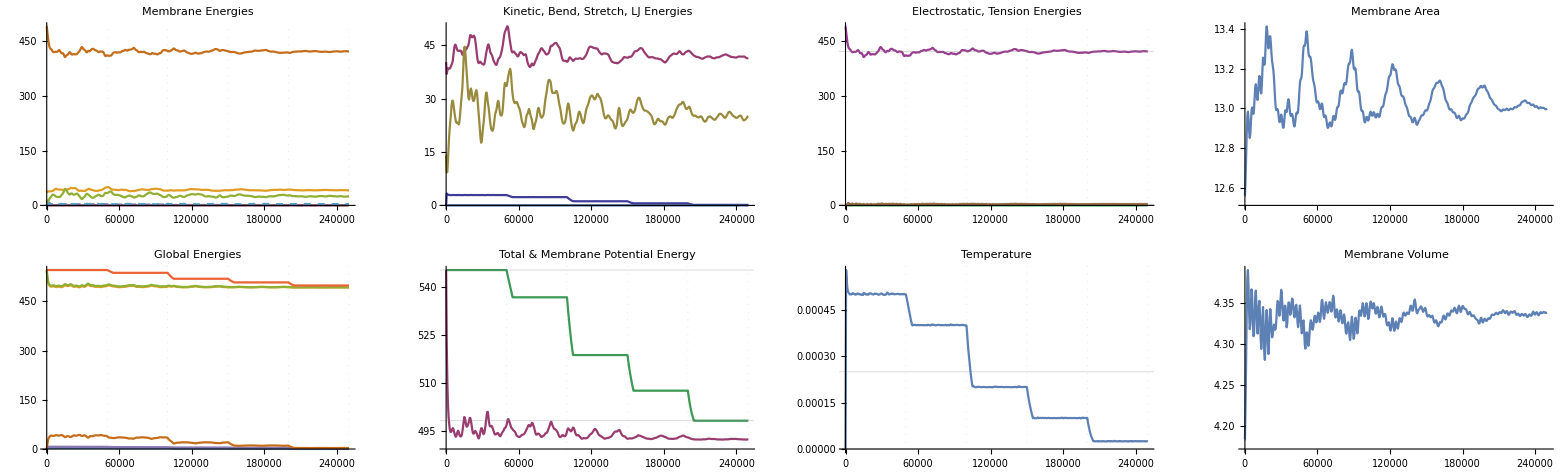
-Graphics-Temporal Evolution Plots

 | Thermostat
C_L | 5.
T_0^tg | 0.0005
Q | n
Anneal | y
a_freq | 50000.
a_dur | 5000.
f_T^ann | 1.25
f_Q^ann | 1.125
Off-loaded | n
Random | y  | System
N_v | 3872.
r | 20.
q_str | 600.
α | 1.
c_s | 0.001
σ_A | 0.
σ_V | 0.0001
κ_b | 5.
κ_s | 125.
G_con | N
Δt | 0.0005
t_tot | 250000.
t_run | 803.283
r_run | 311.223 | Initial | Final | Drift (Final/Initial) | Mean | Mean Drift (Mean/Initial) | Coeff. Variation
Area | 12.56 | 13. | 1.035 | 13.04 | 1.039 | 0.008019
Volume | 4.183 | 4.338 | 1.037 | 4.334 | 1.036 | 0.003048
Temperature | 0 | 0.00002442 | Round[∞,∞] | 0.0002491 | Round[∞,∞] | 0.7216
Total Energy | 545.4 | 498.3 | 0.9136 | 521.8 | 0.9567 | 0.03364
Local Potential | 545.4 | 492.5 | 0.9029 | 494.2 | 0.906 | 0.004597
Kinetic | 0 | 0.1418 | Round[∞,∞] | 1.447 | Round[∞,∞] | 0.7216
Bending | 40.27 | 41.36 | 1.027 | 42.34 | 1.051 | 0.04477
Stretching | 14.19 | 25.05 | 1.766 | 26.47 | 1.865 | 0.1493
Surface Tension | 0 | 0 | Round[∞,∞] | 0 | Round[∞,∞] | Round[∞,∞]
LJ-E | 0 | 0 | Round[∞,∞] | 0 | Round[∞,∞] | Round[∞,∞]
ES-E | 491. | 422.3 | 0.8601 | 421.8 | 0.8591 | 0.01272
Volume Tension | 0 | 3.779 | Round[∞,∞] | 3.6 | Round[∞,∞] | 0.1632Temporal Information

Click for simulation movie in Ovito.

Click to open directory.Click to copy directory path.

```mathematica
(* The following function plots the time series for all relevant thermodynamic and geometric quantities of interest: *)
simPlot@janus4Stripes
```

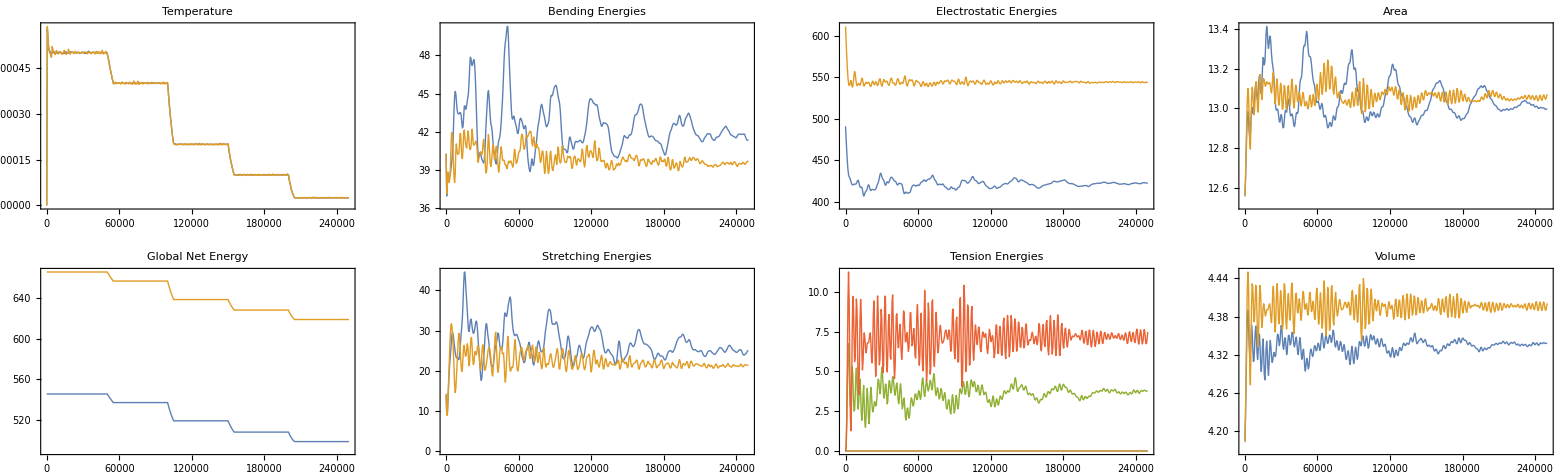

```mathematica
(* The following operates on lists of mutliple simulations to compare series data.  Ignore the top 4 plots, which are empty because there is no salt or tension differences between these simulations: *)
setPlot@{janus4Stripes,janus5Stripes}
```

```mathematica
(* Run this to load the correct mesh file, here 3-18 (the latter argument is the discretization number) [you must point the DownValue (function definition) to this file, that is not manual] : *)
loadMesh[18]
```

```mathematica
(* This produces a charge-highlighted visualization of the mesh: *)
staticSim/@{janus4Stripes, janus5Stripes}//Row
```

-Graphics3D--Graphics3D-

```mathematica
(* This produces the electrostatic energy-highlighted visualization of the mesh: *)
staticSimEnergies/@{janus4Stripes, janus5Stripes}//Row
```

-Graphics3D--Graphics3D-

```mathematica
(* This produces the elastic energy-highlighted visualization of the mesh: *)
staticSimEnergies[#,"local_elastic_E.off"]&/@{janus4Stripes, janus5Stripes}//Row
```

-Graphics3D--Graphics3D-

## § Post-Optimization: Counterion Condensation Setup

We assume the shape to be negatively charged, thus counterions are positive (cationic) and have the diameter & mass of Na^+, scaled up to account for hydration radius (σ_ion=0.3nm).    Anionic coions will be taken to have the same size and mass for simplicity.

The following generates a finer mesh (the original mesh, plus its dual) in order to make a counterion-impermeable membrane of a given shape.

It then does all preliminary calculations in preparation to generate a LAMMPS data file and input script, and exports each.

LAMMPS Data File Generation

## Preliminary Calculations

```mathematica
(* Particle details, unit calcculations, box size calculation, etc: *)
σRefReal=20; 
σMeshPtReal=2*0.3;
σMic1Real=2*0.3; (* Diameter of Na^+ *)
σMic2Real=2*0.3;
qMic1Bare=1;
qMic2Bare=-1;
mMic1Real=22.9898;  (* Na mass, g/mol. *)
mMeshPtReal=22.9898;
mMic2Real=22.9898; (* Chloride mass, g/mol *)
	(* Reduced equivalents: *)
	σRef=1; 
	σMeshPt=(σMeshPtReal/σRefReal);	
	σMic1=(σMic1Real/σRefReal);
	σMic2=(σMic2Real/σRefReal);
	mMeshPt=(mMeshPtReal/mMic1Real);
	mMic1=(mMic1Real/mMic1Real);
	mMic2=(mMic2Real/mMic1Real);

(* Simulation box details: *)
boxLengthReal=QuantityMagnitude[UnitConvert[L/.Solve[L^3==100*4π Quantity[N@σRefReal,"Nanometers"]^3,L]//Last,"Nanometers"]];
myOutBox={Opacity[0.3],Cuboid[-(boxLengthReal/2){1,1,1},(boxLengthReal/2)*{1,1,1}]};
	(* Reduced equivalents: *)
	boxL=(boxLengthReal/σRefReal);
	myInBox={Opacity[0.3],Cuboid[-(boxL/2){1,1,1},(boxL/2)*{1,1,1}]};
```

```mathematica
(* Running the staticSim function creates a fullCoords containing both the optimziation basic mesh and its dual coordinates: *)
loadMesh[18]
staticSim[janus4Stripes,0];
```

```mathematica
Graphics3D[{{(*myInBox,*)Sphere[fullCoords,0.5σMic1],{Red,Sphere[fullCoordsCharged,0.5σMic1]}(*,{Yellow,Specularity[White,50],Sphere[#,.5σMic1]}&/@counterInits*)}},Boxed->False,ViewPoint->{Pi,-2Pi,Pi/2},ImageSize->750]
```

-Graphics3D-

## Random Ion Enumeration

```mathematica
(* Initiaiting the list of counterions and counting it: *)
micro1Inits={};micro2Inits={};

micro1Inits//Length//Dynamic
micro2Inits//Length//Dynamic
```

```mathematica
(* This enumerates positions of the counterions/cations (type 1, modeled as Na^+); positions are rejected under significant overlap: *)
With[{xAxisBound=Max[(Abs[#⟦1⟧]&/@fullCoords)]+σMic1,yAxisBound=Max[(Abs[#⟦2⟧]&/@fullCoords)]+σMic1,zAxisBound=Max[(Abs[#⟦3⟧]&/@fullCoords)]+σMic1},
While[Length[micro1Inits]<Round[Total@fullCharges](*(Abs[qMeshTot]+totNumSaltIons/2)*),s=RandomReal[{(-boxL/2+σMic1/2),(boxL/2-σMic1/2)},3];
If[And[
And@@(Norm[#-s]>1.5σMic1&/@micro1Inits),
And@@(Norm[#-s]>1.5((σMic1+σMic2)/2)&/@micro2Inits),
((s⟦1⟧<-xAxisBound)||(xAxisBound<s⟦1⟧))&&((s⟦2⟧<-yAxisBound)||(yAxisBound<s⟦2⟧))&&((s⟦3⟧<-zAxisBound)||(zAxisBound<s⟦3⟧))],
AppendTo[micro1Inits,s]]]];
```

```mathematica
(* Visualization of the mesh, its discretized points, and the random initial state for counterions (all to scale): *)
Show[Graphics3D[{{myInBox,{Opacity[1.0],Sphere[fullCoords,σMic1/2]},{Red,Sphere[fullCoordsCharged,σMic1/2]},{Blue,Specularity[White,50],Sphere[#,.5σMic1]}&/@micro1Inits,{Red,Specularity[White,50],Sphere[#,.5σMic2]}&/@micro2Inits}},Boxed->False,ViewPoint->{Pi,-2Pi,Pi/2},ImageSize->750](*,ℛ*)]
```

-Graphics3D-

## Final Data File Exporting

The charge is specified within the data file.  The following uses the function qLJ within NBTools.wl to get the units correct:

```mathematica
(* Generate subset of the output for the mesh separately: *)
meshOutput=Table[{i,1}~Join~fullCoords⟦i⟧~Join~{qLJ[fullCharges⟦i⟧,σRefReal]}~Join~{σMeshPt,mMeshPt/(4/3. π (σMeshPt)^3)},{i,1,Length@fullCoords}];
```

```mathematica
(* The output for the data file (with per-vertex charge): *)
output=
Flatten[{OutputForm/@{
"LAMMPS data file",
ToString[Length[fullCoords]+Length[micro1Inits]+Length[micro2Inits]]<>" atoms",
"3 atom types",
ToString[-boxL/2]<>" "<>ToString[boxL/2]<>" xlo xhi",
ToString[-boxL/2]<>" "<>ToString[boxL/2]<>" ylo yhi",
ToString[-boxL/2]<>" "<>ToString[boxL/2]<>" zlo zhi","",
"Atoms",""},
{meshOutput},
{With[{typeLabeled=micro1Inits/.{x_,y_,z_}:>{2,x,y,z,q,d,ρ}},
Flatten/@Thread[{Length[fullCoords]+Range[Length[micro1Inits]],typeLabeled}]]/.{q->-qLJ[1,σRefReal],d:>σMic1,ρ:>mMic1/(4/3 π(.5 σMic1Real/σRefReal)^3)}},
{With[{typeLabeled=micro2Inits/.{x_,y_,z_}:>{3,x,y,z,-1,d,ρ}},
Flatten/@Thread[{Length[fullCoords]+Length[micro1Inits]+Range[Length[micro2Inits]],typeLabeled}]]/.{q->0,d:>σMic2,ρ:>mMic2/(4/3 π(.5 σMic2Real/σRefReal)^3)}}},2];
```

```mathematica
(* Export the final data file to the current directory: *)
Export["initCoords.ShapeCondensation",output,"Table","FieldSeparators"->" "];
```

```mathematica
SystemOpen@Directory[]
```

LAMMPS Script File Generation

```mathematica
(* Command to generate an input script using the following parameterization: *)
script[netSteps_:1000,dumpInt_:1000000,thermoInt_:10000,timeStep_:2.5*10^-4]:=
Block[{instDInt=5*dumpInt},

scriptText=
{{"# 3D simulation of ion condensation on nanomembrane"},{},

{"units lj"},
{"boundary p p p"},
{"atom_style hybrid charge sphere"},
{"neighbor",0.3,"bin"},
{"neigh_modify","every",1,"delay",0,"check","yes"},
{"neigh_modify","exclude","type",1,1},
{"neigh_modify","page",400000},
{"neigh_modify","one",40000},{},

{"## Create Simulation Box, Atoms ##"},
{"read_data","initCoords.ShapeCondensation"},{},

{"## Group Atoms by Type ##"},
{"group mesh type",1},
{"group micro1 type",2},
{"group micro2 type",3},{},

{"## Defining Particle/Medium Properties ##"},
{"mass",1,1, "# mass of mesh points, immobile, irrelevant."},
{"mass",2,1,"# reduced mass of counterions (Na)"},
{"mass",3,1, "# using same mass as (Na)"},

{"dielectric",78.54},{},

{"## Ascribing Initial Velocities ##"},
{"velocity","all","create",1.,4928459,"rot","yes","dist","gaussian","units","box","# 1-kB*T,random seed,zero net ang.mom.,gauss from MB stats"},{},

{"## Ascribing interparticle potentials: ##"},
{"pair_style","lj/long/coul/long","cut","long",2^(1/6.)σMic1,(boxL/2.)},
{"pair_coeff",1,1,1,σMeshPt,0,"# epsilon, sigma, lj_cut"},
{"pair_coeff",1,2,1,((σMeshPt+σMic1)/2),2^(1/6.)((σMeshPt+σMic1)/2)},
{"pair_coeff",1,3,1,((σMeshPt+σMic2)/2),2^(1/6.)*((σMeshPt+σMic2)/2)},
{"pair_coeff",2,2,1,σMic1,(2^(1/6.)*σMic1)},
{"pair_coeff",2,3,1,((σMic1+σMic2)/2),2^(1/6.)*((σMic1+σMic2)/2)},
{"pair_coeff",3,3,1,σMic2,(2^(1/6.)σMic2)},
{"pair_modify","shift","yes","# the additive e_LJ for repulsion-only"},{},

{"kspace_style","pppm/disp","0.00001"},

{"## Ensemble Fixes (+ for output) ##"},
{"variable","myTStep","equal",FortranForm[N@timeStep]},
{"timestep","${myTStep}"},
{"variable","myDStep","equal",FortranForm[Round@dumpInt]},
{"fix","myMicro1Fix","micro1","nvt","temp",1.0,1.0,N[100*timeStep],"# T_start, T_stop, T_damp=100*timestep"},
{"fix","myMicro2Fix","micro2","nvt","temp",1.0,1.0,N[100*timeStep],"# T_start, T_stop, T_damp=100*timestep"},{},

{"## Define Computes for Output ##"},
{"compute","myMeshT","mesh","temp"},
{"compute","myMicro1T","micro1","temp"},
{"compute","myMicro2T","micro2","temp"},
{"compute","meshPotVec","mesh","pe/atom"},
{"compute","myMeshPot","mesh","reduce","sum","c_meshPotVec"},
{"compute","mic1PotVec","micro1","pe/atom"},
{"compute","myMicro1Pot","micro1","reduce","sum","c_mic1PotVec"},
{"compute","mic2PotVec","micro2","pe/atom"},
{"compute","myMicro2Pot","micro2","reduce","sum","c_mic2PotVec"},
{"compute","atomPot ","all","pe/atom"},
{"compute","atomKin ","all","ke/atom"},{},

{"## Defining Output Information ##"},
{"dump","posD","all","custom","${myDStep}","dump.melt","id","type","x","y","z","q","c_atomPot","c_atomKin"},
{"dump","posDMicro1","micro1","custom",FortranForm@Round[dumpInt/5],"dumpMicro1Only.melt","id","type","x","y","z","q","c_atomPot","c_atomKin"},
{"dump","posDMicro2","micro2","custom",FortranForm@Round[dumpInt/5],"dumpMicro2Only.melt","id","type","x","y","z","q","c_atomPot","c_atomKin"},{},

{"thermo_style","custom","step","temp","c_myMeshT","c_myMicro1T","c_myMicro2T","c_myMeshPot","c_myMicro1Pot","c_myMicro2Pot","etotal","ke","pe","vol","press"},
{"thermo",Round[thermoInt,1]},{},

{"restart",Round[0.1*netSteps,1],"assemblyRestart.*","# creates 10 restart files throughout run"},
{"run",Round[netSteps,1]},{},

{"unfix","myMicro1Fix"},
{"unfix","myMicro2Fix"},
{"uncompute","myMeshT"},
{"uncompute","myMicro1T"},
{"uncompute","myMicro2T"},
{"uncompute","meshPotVec"},
{"uncompute","myMeshPot"},
{"uncompute","mic1PotVec"},
{"uncompute","myMicro1Pot"},
{"uncompute","mic2PotVec"},
{"uncompute","myMicro2Pot"},
{"uncompute","atomPot"},
{"uncompute","atomKin"},
{"undump","posD"}}]
```

```mathematica
Export["ShapeCondensation.script",script[1500000,1000,100,2.5*10^-4],"Table"]
```

ShapeCondensation.script

```mathematica
SystemOpen@Directory[]
```

## § Analytical Manning Condensation Calculations

The following functions are to conduct analytical calculations using the Manning model valid for homogeneously charged systems.

Notably, this does not use the unit framework in Mathematica and the user must keep track of units manually.

Use cases are sprinkled throughout, including calculation reproducing the Figures from both the Jadhao PRE (see homogeneously charged section) and Brunk & Jadhao JMCB (see equipotential surface section) papers.

This section could generally use cleaned up, but should be functional.

Common Geometric Functions

## Generic

```mathematica
bjerrumL=0.714;
ClearAll@s;

(* Useful function in this geometry [Eqn S36 in SI]: *)
s[e_]:=If[e==0,2,1+(1-e*e)/e ArcTanh[e]]
```

```mathematica
(* Parameters for the thermal de Broglie wavelength computation: *)
Quantity[22.9,("Grams")/("Moles")] Na^-1 //QuantityMagnitude;
hPlanck=UnitConvert[Quantity[6.62607004×10^-34,(("Meters")^2"Kilograms")/("Seconds")],(("Meters")^2"Grams")/("Seconds")]//QuantityMagnitude;
Solve[1/2 Quantity[22.9,("Grams")/("Moles")] Na^-1 v^2==3/2 kB Quantity[298,"Kelvins"],v];
```

```mathematica
(* The shape area as a function of aspect ratio: *)
shapeArea[λ_,R0_:10]:=Which[
λ≤1,oblateArea[√(1-λ^2),oblateAFixedV[√(1-λ^2),R0]],
λ>1,prolateArea[(√(λ^2-1))/λ,prolateCFixedV[(√(λ^2-1))/λ,R0]]]
```

## Sphere

```mathematica
(* The area of the sphere {radius}: *)
sphereArea[R0_]:=4π R0^2

(* The charge density of the sphere {net charge, radius}: *)
σSphere[Q_,R0_]:=Q/sphereArea[R0]
(* The Gouy-Chapman length (condensed layer thickness) {charge, eccentricity, axial radius}: *)
gcLengthSphere[Q_,R0_]:=1/(2π*bjerrumL*σSphere[Q,R0])

(* Manning radius, ratio of the ellipse dimension to the thickness of the condensed layer: *)
ManningRSphere[Q_,R0_]:=R0/gcLengthSphere[Q,R0]
```

## Oblate (Disks)

```mathematica
(* Area of the oblate disk {eccentricity, axial radius} [Eqn S35 in SI]: *)
oblateArea[e_,a_]:=If[e==0,4*π*a*a,2*π*a*a*s[e]]

(* Volume of the oblate disk {eccentricity, axial radius}: *)
oblateVolume[e_,a_]:=(4/3)*π*a^3*√(1-e^2)

(* Eccentricity of an oblate disk {aspect ratio}: *)
eOblate[λ_]:=√(1-λ^2)

(* Axial (a) with fixed volume {eccentricity, spherical equivalent radius} [Eqn S43 in SI, Eqn 30 in PRE]: *)
oblateAFixedV[e_,R0_]:=R0/(1-e^2)^(1/6)

(* Charge density of the disk {charge, eccentricity, axial radius}: *)
σOblate[Q_,e_,a_]:=Q/oblateArea[e,a]
(* The Gouy-Chapman length (condensed layer thickness) {charge, eccentricity, axial radius}: *)
gcLengthOblate[Q_,e_,a_]:=1/(2π*bjerrumL*σOblate[Q,e,a])

(* Manning radius, ratio of the ellipse dimension to the thickness of the condensed layer: *)
ManningROblate[Q_,e_,a_]:=a/gcLengthOblate[Q,e,a]
```

## Prolate (Rods)

```mathematica
(* The area of a prolate as function of eccentricity & longest axis (c) [Eqn 7-8 of PRE]: *)
prolateArea[e_,c_]:=If[e==0,4 π c^2,2π*c^2*√(1-e^2)*(√(1-e^2)+ArcSin[e]/e)]

(* The eccentricity of the prolate as a function of {aspect ratio}: *)
eProlate[λ_]:=√(1-(1/λ)^2)

(* The longest axis for a fixed volume as a function of {eccentricity, would-be-sphere radius} [Eqn 27 from PRE]: *)
prolateCFixedV[e_,R0_]:=R0/(1-e^2)^(1/3)

(* Expression for the bare charge density on the prolate spheroid: *)
σProlate[Q_,e_,c_]:=Q/prolateArea[e,c]

(* The Gouy-Chapman length (condensed layer thickness) {charge, eccentricity, axial radius}: *)
gcLengthProlate[Q_,e_,c_]:=1/(2π*bjerrumL*σProlate[Q,e,c])

(* Manning radius, ratio of the ellipse dimension to the thickness of the condensed layer: *)
ManningRProlate[Q_,e_,c_]:=c/gcLengthProlate[Q,e,c]
```

Equipotential Surface (Conducting)

## Reference Sphere

```mathematica
(* The equipotential (conducting) spherical ES energy {charge, radius}: *)
equiSphereU[Q_,R0_]:=Q^2/(2R0)

(* The reduced equivalent:  *)
equiSphereUStar[Q_,R0_]:=bjerrumL*equiSphereU[Q,R0]
```

```mathematica
(* Compute the condensation fraction α {eccentricity, packing fraction}: *)
αSphere[η_,Q_,R0_:10]:=Block[{k=(2/3)*(ManningRSphere[Q,R0]/η)*(1/2),ξ=2*equiSphereUStar[Q,R0]},
x/.FindRoot[k*(x/(1-x))-Exp[ξ((1-x)/Q)],{x,0},PrecisionGoal->4,AccuracyGoal->4,MaxIterations->Infinity]]
```

```mathematica
(* Compute the reduced potential after condensation: *)
sphereUStarPostCond[Q_,R0_,η_]:=equiSphereUStar[Q(1-αSphere[η,Q,R0]),R0]

(* Compute the total free energy of the system *)
ℱSphere[η_,Q_,R0_:10]:=Block[{α=αSphere[η,Q,R0],b=gcLengthSphere[Q,R0],𝒜=sphereArea[R0],Ω=(4/3)π R0^3,Vws=Ω/η,Λ=hPlanck/(3.8027233477250085*10^-23*569.722)(* mass per sodium ion, mean thermal velocity *)},

sphereUStarPostCond[Q,R0,η]+α(Q Log[(α Q Λ^3)/(𝒜*b)]-Q)+(1-α)(Q Log[((1-α)Q Λ^3)/Vws]-Q)]
```

## Oblate (Disks)

```mathematica
(* The equipotential (conducting) oblate ES energy {charge, eccentricity, radius}: *)
equiOblateU[Q_,e_,a_]:=If[e==0,Q^2/(2a),(Q^2/(2a*e))ArcTan[e/(√(1-e^2))]]
(* The reduced equivalent (also enforcing the volume constraint):  *)
equiOblateUStar[Q_,e_,R0_]:=bjerrumL*equiOblateU[Q,e,oblateAFixedV[e,R0]]
```

```mathematica
(* Compute the condensation fraction α {eccentricity, packing fraction, charge of the vertices, number of vertices}: *)
αOblateEqui[e_,η_,Q_,R0_:10]:=Block[{k=(2/3)*(ManningROblate[Q,e,oblateAFixedV[e,R0]]/η)*((1-e^2)^(1/2)/s[e]),ξ=2*equiOblateUStar[Q,e,R0]},
x/.FindRoot[k*(x/(1-x))-Exp[ξ((1-x)/Q)],{x,0},PrecisionGoal->4,AccuracyGoal->4,MaxIterations->Infinity]]
```

```mathematica
(* Compute the total free energy of the system *)
ℱOblateEqui[e_,η_,Q_,R0_:10]:=Block[{α=αOblateEqui[e,η,Q,R0],b=gcLengthOblate[Q,e,oblateAFixedV[e,R0]],𝒜=oblateArea[e,oblateAFixedV[e,R0]],Ω=(4/3)π R0^3,Vws=Ω/η,Λ=hPlanck/(3.8027233477250085*10^-23*569.722)(* mass per sodium ion, mean thermal velocity *)},

equiOblateUStar[Q (1-α),e,R0]+α(Q Log[(α Q Λ^3)/(𝒜*b)]-Q)+(1-α)(Q Log[((1-α)Q Λ^3)/Vws]-Q)]
```

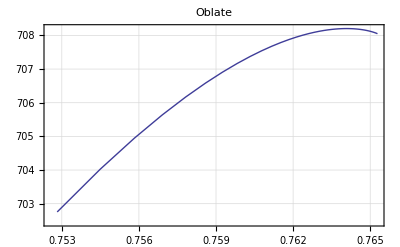
-Graphics-Condensation Fraction αEnergy U^*

```mathematica
labelPlot[
ListLinePlot[
Table[With[{α=αOblateEqui[e,10^-3,600]},
{α,equiOblateUStar[600(1-α),e,10]}],{e,0.01,0.95,0.01}],
PlotLabel->myStyle@"Oblate",PlotRange->All,PlotStyle->Thick,FrameTicksStyle->Directive[Black,16]],
{"Condensation Fraction α","Energy U^*"}]
```

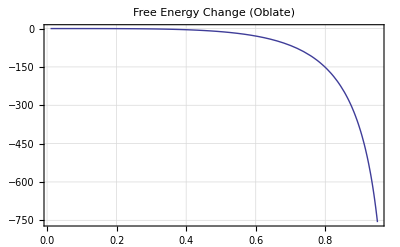
-Graphics-edℱ

```mathematica
(* Plotting the Δℱ at (η = 10^-4) [agrees with Fig. S6 in SI, orange curve]: *)
labelPlot[Plot[{ℱOblateEqui[e,10^-12,600]-ℱSphere[10^-12,600]},{e,0.01,0.95},PlotRange->All,PlotLabel->myStyle@"Free Energy Change (Oblate)",PlotStyle->Thick,PlotLegends->None],{"e","dℱ"}]
```

## Prolate (Rods)

```mathematica
(* The equipotential (conducting) prolate ES energy {charge, eccentricity, radius}: *)
equiProlateU[Q_,e_,c_]:=If[e==0,Q^2/(2c),(Q^2/(2c*e))*ArcTanh[e]]
(* The electrostatic energy of an equipotential (conducting) prolate of a fixed volume as a function {eccentricity, sphere radius, net charge}: *)
equiProlateUstar[Q_,e_,R0_:10]:=bjerrumL*equiProlateU[Q,e,prolateCFixedV[e,R0]]
```

```mathematica
(* Compute the condensation fraction α {eccentricity, packing fraction, charge of the vertices, number of vertices}: *)
αProlateEqui[e_,η_,Q_,R0_:10]:=Block[{k=(2/3)*(ManningRProlate[Q,e,prolateCFixedV[e,R0]]/η)*((1-e^2)^(1/2)/s[e]),ξ=2*equiProlateUstar[Q,e,R0]},
x/.FindRoot[k*(x/(1-x))-Exp[ξ((1-x)/Q)],{x,0},PrecisionGoal->4,AccuracyGoal->4,MaxIterations->Infinity]]
```

```mathematica
(* Compute the total free energy of the system: *)
ℱProlateEqui[e_,η_,Q_,R0_:10]:=Block[{α=αProlateEqui[e,η,Q,R0],b=gcLengthProlate[Q, e, prolateCFixedV[e,R0]],𝒜=prolateArea[e,prolateCFixedV[e,R0]],Ω=(4/3)π R0^3,Vws=Ω/η,Λ=hPlanck/(3.8027233477250085*10^-23*569.722)},

equiProlateUstar[Q (1-α),e,R0]+α(Q Log[(α Q Λ^3)/(𝒜*b)]-Q)+(1-α)(Q Log[((1-α)Q Λ^3)/Vws]-Q)]
```

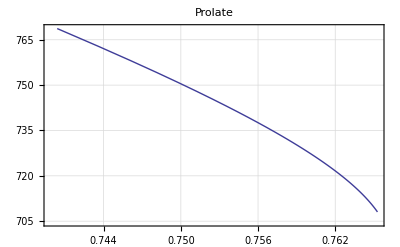
-Graphics-Condensation Fraction αEnergy U^*

```mathematica
labelPlot[
ListLinePlot[
Table[With[{α=αProlateEqui[e,10^-3,600,10]},
{α,equiProlateUstar[600(1-α),e,10]}],{e,0.01,0.95,0.01}],
PlotLabel->myStyle@"Prolate",PlotRange->All,PlotStyle->Thick,FrameTicksStyle->Directive[Black,16]],
{"Condensation Fraction α","Energy U^*"}]
```

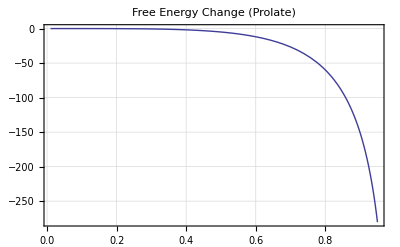
-Graphics-edℱ

```mathematica
labelPlot[Plot[{ℱProlateEqui[e,10^-4,600]-ℱSphere[10^-4,600]},{e,0.01,0.95},PlotRange->All,PlotLabel->myStyle@"Free Energy Change (Prolate)",PlotStyle->Thick,PlotLegends->None],{"e","dℱ"}]
```

```mathematica
Block[{η=10^-4,Q=600},
sphereRef=ℱSphere[η,Q];
labelPlot[Plot[{ℱOblateEqui[e,η,Q]-sphereRef,ℱProlateEqui[e,η,Q]-sphereRef},{e,0.01,0.95},PlotRange->All,PlotLabel->myStyle@"Free Energy Change (Prolate)",PlotStyle->Thick,PlotLegends->None],{"e","dℱ"}]]
```

## Combined (with respect to λ instead of e, adding surface tension)

```mathematica
(* The electrostatic potential vs. aspect ratio: *)
uStar[λ_,Q_,R0_]:=Which[
λ≤1,equiOblateUStar[Q,√(1-λ^2),R0],
λ>1,equiProlateUstar[Q,(√(λ^2-1))/λ,R0]]

uReal[λ_,Q_,R0_]:=bjerrumL^-1 uStar[λ,Q,R0]
netUShapeReal[λ_,Q_,R0_,σ_]:=uReal[λ,Q,R0]+0.24305278499015862*σ*shapeArea[λ]
netUShapeStar[λ_,Q_,R0_,σ_]:=bjerrumL*uReal[λ,Q,R0]+0.24305278499015862*σ*shapeArea[λ]

(* Manning Condensation model: *)

(* The (ES-only) free energy difference between the shape and the reference sphere: *)
ℱShapeDiffEqui[λ_,η_,Q_,R0_:10]:=Which[
λ≤1,ℱOblateEqui[√(1-λ^2),η,Q,R0]-ℱSphere[η,Q,R0],
λ>1,ℱProlateEqui[(√(λ^2-1))/λ,η,Q,R0]-ℱSphere[η,Q,R0]]
(* The net shape free energy (with surface tension, numerical coefficient = 1 (dyn/cm) in ((Subscript[k, B] T)/nm^2)) {aspect ratio, packing fraction, tension coefficient, vertex charge, number of vertices}: *)
netℱShapeDiffEqui[λ_,η_, σ_,Q_,R0_:10]:=(ℱShapeDiffEqui[λ,η,Q,R0]+0.24305278499015862*σ*shapeArea[λ,R0])-0.24305278499015862*σ*shapeArea[1,R0]
```

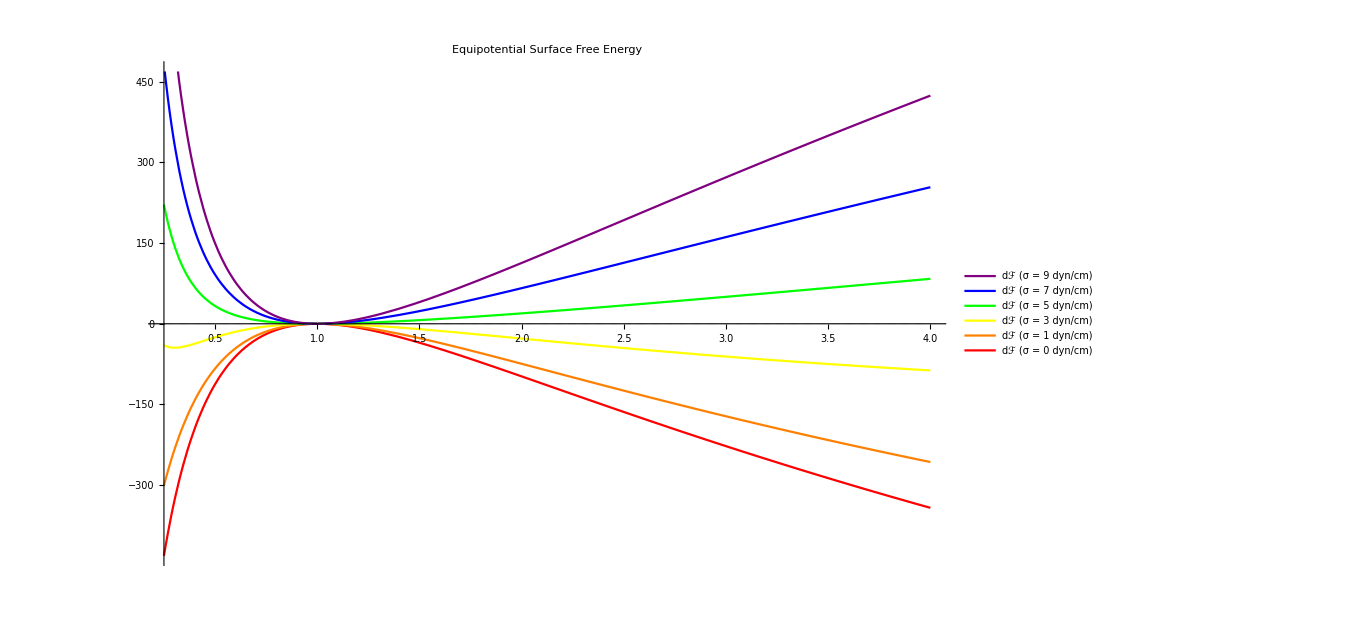
-Graphics-Aspect Ratio λdℱ (k_BT)

```mathematica
manningEquiTensionPlot=
labelPlot[Plot[Evaluate@Table[netℱShapeDiffEqui[λ,10^-3,σ,600],{σ,{0,1,3,5,7,9}}],{λ,0.25,4},PlotStyle->{{Thick,Red},{Thick,Orange},{Thick,Yellow},{Thick,Green},{Thick,Blue},{Thick,Purple}},PlotLabel->myStyle@"Equipotential Surface Free Energy",GridLines->{None,{0}},GridLinesStyle->Dashed,FrameTicksStyle->Directive[Black,16,FontFamily->"Times New Roman"],PlotLegends->Placed[LineLegend[myStyle/@Table["dℱ (σ = "<>ToString[σ]<>" dyn/cm)",{σ,{0,1,3,5,7,9}}],LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->Gray,Background->White]&),LegendMargins->1,LegendLayout->"ReversedColumn"],Scaled[{{.2375,.285}}]],ImageSize->1000],{"Aspect Ratio λ","dℱ (k_BT)"}]
```

```mathematica
Export["FreeEnergy_WithTension_EquipotentialSurface.png",manningEquiTensionPlot]
```

FreeEnergy_WithTension_EquipotentialSurface.png

## Analytical Calculations (from Brunk & Jadhao JMCB)

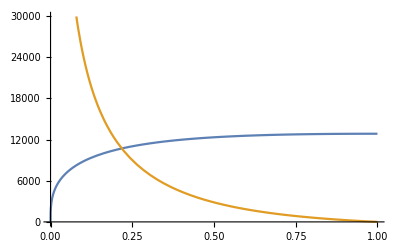

```mathematica
(* Plot of Subscript[U, oblate]^*(λ) and the derivative: *)
With[{Q=600,a=10},Plot[{equiOblateUStar[Q,√(1-λ^2),a],D[equiOblateUStar[Q,√(1-λ^2),a],λ]//Evaluate},{λ,0,1},PlotLegends->None]]
```

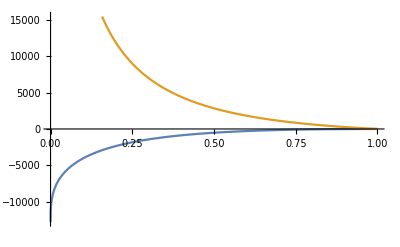

```mathematica
(* Plot of Subscript[U, oblate]^*(λ) and the derivative: *)
With[{Q=600,a=10},Plot[{equiOblateUStar[Q,√(1-λ^2),a]-equiSphereUStar[Q,a],D[equiOblateUStar[Q,√(1-λ^2),a]-equiSphereUStar[Q,a],λ]//Evaluate},{λ,0,1},PlotLegends->None]]
```

```mathematica
(* Components of the final disk energy expression: *)
equiOblateUStar[Q,√(1-λ^2),a]
oblateArea[√(1-λ^2),oblateAFixedV[√(1-λ^2),a]]
s[√(1-λ^2)]
```

0.714 If[√(1-λ^2)==0,Q^2/((2 a)/((λ^2)^(1/6))),(Q^2 ArcTan[(√(1-λ^2))/(√(1-(√(1-λ^2))^2))])/((2 a √(1-λ^2))/((λ^2)^(1/6)))]

If[√(1-λ^2)==0,(4 π a a)/((λ^2)^(1/6) (λ^2)^(1/6)),(2 π a a s[√(1-λ^2)])/((λ^2)^(1/6) (λ^2)^(1/6))]

If[√(1-λ^2)==0,2,1+((1-√(1-λ^2) √(1-λ^2)) ArcTanh[√(1-λ^2)])/(√(1-λ^2))]

```mathematica
(Q^2 ArcTan[(√(1-λ^2))/(√(1-(√(1-λ^2))^2))])/((2 a √(1-λ^2))/((λ^2)^(1/6)))+σ*((2 π a a (1+((1-√(1-λ^2) √(1-λ^2)) ArcTanh[√(1-λ^2)])/(√(1-λ^2))))/((λ^2)^(1/6) (λ^2)^(1/6)))
```

```mathematica
Limit[(Q^2 (λ^2)^(1/6) ArcTan[(√(1-λ^2))/(√(λ^2))])/(2 a √(1-λ^2))+(2 a^2 π σ (1+(λ^2 ArcTanh[√(1-λ^2)])/(√(1-λ^2))))/((λ^2)^(1/3)),λ->0]
```

σ ∞ Sign[a]^2

```mathematica
Limit[equiOblateUStar[600,√(1-λ^2),10],λ->0]
```

0.

```mathematica
(* Components of the final disk energy expression: *)
equiProlateUstar[Q,(√(λ^2-1))/λ,a]
prolateArea[(√(λ^2-1))/λ,prolateCFixedV[(√(λ^2-1))/λ,a]]
s[(√(λ^2-1))/λ]
```

0.714 If[(√(-1+λ^2))/λ==0,Q^2/((2 a)/((1-(-1+λ^2)/λ^2)^(1/3))),(Q^2 ArcTanh[(√(-1+λ^2))/λ])/((2 a √(-1+λ^2))/((1-(-1+λ^2)/λ^2)^(1/3) λ))]

If[(√(-1+λ^2))/λ==0,4 π (a/((1-(-1+λ^2)/λ^2)^(1/3)))^2,2 π (a/((1-(-1+λ^2)/λ^2)^(1/3)))^2 √(1-((√(-1+λ^2))/λ)^2) (√(1-((√(-1+λ^2))/λ)^2)+ArcSin[(√(-1+λ^2))/λ]/((√(-1+λ^2))/λ))]

If[(√(-1+λ^2))/λ==0,2,1+((1-(√(-1+λ^2) √(-1+λ^2))/(λ λ)) ArcTanh[(√(-1+λ^2))/λ])/((√(-1+λ^2))/λ)]

```mathematica
Limit[(Q^2 ArcTanh[(√(-1+λ^2))/λ])/((2 a √(-1+λ^2))/((1-(-1+λ^2)/λ^2)^(1/3) λ))+σ(2 π (a/((1-(-1+λ^2)/λ^2)^(1/3)))^2 √(1-((√(-1+λ^2))/λ)^2) (√(1-((√(-1+λ^2))/λ)^2)+ArcSin[(√(-1+λ^2))/λ]/((√(-1+λ^2))/λ))),λ->∞]
```

σ ∞ Sign[a]^2

```mathematica
Assuming[{λ>0},FullSimplify[(Q^2 ArcTanh[(√(-1+λ^2))/λ])/((2 a √(-1+λ^2))/((1-(-1+λ^2)/λ^2)^(1/3) λ))]+σ FullSimplify[2 π (a/((1-(-1+λ^2)/λ^2)^(1/3)))^2 √(1-((√(-1+λ^2))/λ)^2) (√(1-((√(-1+λ^2))/λ)^2)+ArcSin[(√(-1+λ^2))/λ]/((√(-1+λ^2))/λ))]]//TraditionalForm
```

(2 π a^2 σ ((λ^2 csc^-1(λ/(√(λ^2-1))))/(√(λ^2-1))+1))/λ^(2/3)+(λ^(1/3) Q^2 log(√(λ^2-1)+λ))/(2 a √(λ^2-1))

```mathematica
Limit[equiProlateUstar[600,(√(λ^2-1))/λ,10],λ->∞]
```

0.

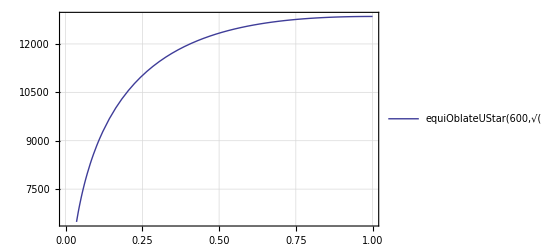

```mathematica
Plot[equiOblateUStar[600,√(1-λ^2),10],{λ,0,1}]
```

Homogeneously Charge Surface

## Oblate (Disks)

### Preliminary Calculations

```mathematica
oblateU6[e_]:=-((ArcSin[e] (1+(1/e-e) ArcTanh[e])^2)/(2 e))-(1/(512 e^11))5 (-3+2 e^2) (3 e √(1-e^2)+(-3+2 e^2) ArcSin[e]) (-e (-3+e^2)+(-3+2 e^2+e^4) ArcTanh[e])^2-(1/(6291456 e^19))(35+8 e^2 (-5+e^2)) (5 e √(1-e^2) (-21+10 e^2)+3 (35+8 e^2 (-5+e^2)) ArcSin[e]) (-210 e+200 e^3-6 e^5+6 (35-45 e^2+9 e^4+e^6) ArcTanh[e])^2 -(1/(2684354560 e^27))13 (-231+378 e^2-168 e^4+16 e^6) (7 e √(1-e^2) (165-160 e^2+28 e^4)+5 (-231+378 e^2-168 e^4+16 e^6) ArcSin[e]) (1155 e-1715 e^3+581 e^5-5 e^7+5 (-1+e) (1+e) (231-189 e^2+21 e^4+e^6) ArcTanh[e])^2
```

### Final Calculations

```mathematica
(* The equipotential (conducting) oblate ES energy {charge, eccentricity, radius}: *)
oblateU[Q_,e_,a_]:=-4*π^2*(σOblate[Q,e,a])^2*a^3*oblateU6[e]
(* The reduced equivalent (also enforcing the volume constraint):  *)
oblateUStar[Q_,e_,R0_]:=bjerrumL*oblateU[Q,e,oblateAFixedV[e,R0]]
```

```mathematica
(* Compute the condensation fraction α {eccentricity, packing fraction, charge of the vertices, number of vertices}: *)
αOblate[e_,η_,Q_,R0_:10]:=Block[{k=(2/3)*(ManningROblate[Q,e,oblateAFixedV[e,R0]]/η)*((1-e^2)^(1/2)/s[e]),ξ=2*oblateUStar[Q,e,R0]},
x/.FindRoot[k*(x/(1-x))-Exp[ξ((1-x)/Q)],{x,0},PrecisionGoal->4,AccuracyGoal->4,MaxIterations->Infinity]]
```

```mathematica
αOblate[eOblate[2],10^-2,600]
```

0.809634+0. ⅈ

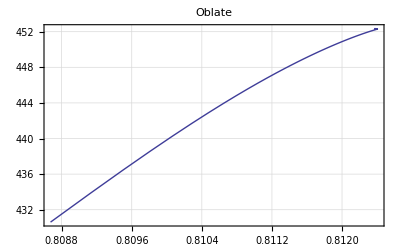
-Graphics-Condensation Fraction αEnergy U^*

```mathematica
labelPlot[
ListLinePlot[
{Table[With[{α=αOblate[e,10^-2,600]},
{α,oblateUStar[600(1-α),e,10]}],{e,0.01,0.95,0.01}]},
PlotLabel->myStyle@"Oblate",PlotRange->All,PlotStyle->Thick,FrameTicksStyle->Directive[Black,16]],
{"Condensation Fraction α","Energy U^*"}]
```

```mathematica
(* Compute the potential after condensation: *)
oblateUStarPostCond[Q_,e_,R0_,η_]:=oblateUStar[Q(1-αOblate[e,η,Q]),e,R0]

(* Compute the total free energy of the system: *)
ℱOblate[e_,η_,Q_]:=Block[{α=αOblate[e,η,Q],b=gcLengthOblate[Q,e,oblateAFixedV[e,10]],𝒜=oblateArea[e,oblateAFixedV[e,10]],Ω=(4/3)π 10^3,Vws=Ω/η,Λ=hPlanck/(3.8027233477250085*10^-23*569.722)(* mass per sodium ion, mean thermal velocity *)},

oblateUStarPostCond[Q,e,10,η]+α(Q Log[(α Q Λ^3)/(𝒜*b)]-Q)+(1-α)(Q Log[((1-α)Q Λ^3)/(Vws - Ω)]-Q)]
```

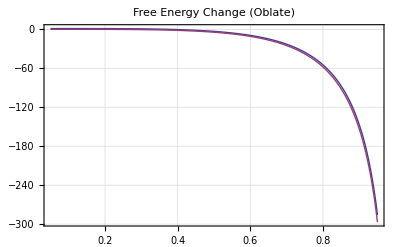
-Graphics-edℱ

```mathematica
(* Plotting the Δℱ at (η = 10^-4) [agrees with Fig. S4 in SI, orange curve]: *)
labelPlot[Plot[{ℱOblate[e,10^-2,600]-ℱSphere[10^-2,600],ℱOblateEqui[e,10^-2,600]-ℱSphere[10^-2,600]},{e,0.05,0.95},PlotRange->All,PlotLabel->myStyle@"Free Energy Change (Oblate)",PlotStyle->Thick,PlotLegends->None],{"e","dℱ"}]
```

## Prolate (Rods)

### Preliminary Calculations

```mathematica
(* Coefficient in the (Eqn 6) expression for Subscript[H, n](e): *)
g[v_,e_]:=Sqrt[1-e^2*(Cos[v])^2]
```

```mathematica
(* Expression for [Eqn 6 in PRE]: *)
Hreq[n_,e_]:=Integrate[g[v,e]*Sin[v]*LegendreP[n,Cos[v]],{v,0,π}]
```

```mathematica
(* The value of Subscript[H, 0](e): *)
	Assuming[0<e<1,Hreq[0,e]]
```

```mathematica
(* The value of Subscript[H, 0](e): *)
Assuming[0<e<1,Hreq[0,e]]
```

√(1-e^2)+ArcSin[e]/e

```mathematica
(* The charge  *)
Assuming[e∈Reals && 0<e<1&&n∈Integers&&n≥0,ProlateQreq[n_,e_]:=1/(2*LegendreP[n,0])*Integrate[LegendreP[n,x]/(√((1/e)^2-1+x^2)),{x,-1,1}]]
```

```mathematica
(* Expression for the summation within (Eqn 5) for the electrostatic energy of a uniformly charged prolate: *)
Prolateop:=Sum[(2n+1)/2* FullSimplify[ProlateQreq[n,e]*LegendreP[n,1/e]]*Hreq[n,e]*Hreq[n,e],{n,0,0,2}]
```

```mathematica
Assuming[0<e<1 && n ∈ Integers, Prolateop]
```

1/2 (√(1-e^2)+ArcSin[e]/e)^2 ArcTanh[e]

```mathematica
(* Solution for the prolate's electrostatic energy keeping up to the 6^th term in the expansion: *)
prolateU6[e_]:=(1/(1572864 e^18))(35-30 e^2+3 e^4) (e √(1-e^2) (-105+110 e^2-8 e^4)+3 (35-60 e^2+24 e^4) ArcSin[e])^2 (5 e (-21+11 e^2)+3 (35-30 e^2+3 e^4) ArcSinh[e/(√(1-e^2))])+(1/(2684354560 e^26))13 (e √(1-e^2) (-1155+1750 e^2-616 e^4+16 e^6)-5 (-231+8 e^2 (63-42 e^2+8 e^4)) ArcSin[e])^2 (7 e (165-170 e^2+33 e^4) (-231+5 e^2 (63-21 e^2+e^4))+5 (231-5 e^2 (63-21 e^2+e^4))^2 ArcSinh[e/(√(1-e^2))])+(1/4) (√(1-e^2)+ArcSin[e]/e)^2 Log[(1+e)/(1-e)]+(1/(512 e^10))5 (-3+e^2) (e √(1-e^2) (-3+2 e^2)+(3-4 e^2) ArcSin[e])^2 (3 (-1+e^2) ArcSinh[e/(√(1-e^2))]+e (3+e Log[-1+2/(1+e)]))
```

### Final Calculations

This assumes the geometric quantities and other invariable terms (Gouy-Chapman length, etc.) were already defined in the equipotential sections.

```mathematica
(* The electrostatic potential of a homogeneously charged oblate ES energy {charge, eccentricity, radius}: *)
prolateU[Q_,e_,c_]:=4*π^2*(σProlate[Q,e,c])^2*c^3*((1-e^2)/e)*prolateU6[e]
(* The reduced equivalent:  *)
prolateUStar[Q_,e_,R0_]:=bjerrumL*prolateU[Q,e,prolateCFixedV[e,R0]]
```

```mathematica
(* Compute the condensation fraction α {eccentricity, packing fraction, charge of the vertices, number of vertices}: *)
αProlate[e_,η_,Q_,R0_:10]:=Block[{k=(2/3)*(ManningRProlate[Q,e,prolateCFixedV[e,R0]]/η)*((1-e^2)^(1/2)/s[e]),ξ=2*prolateUStar[Q,e,R0]},
x/.FindRoot[k*(x/(1-x))-Exp[ξ((1-x)/Q)],{x,0},PrecisionGoal->4,AccuracyGoal->4,MaxIterations->Infinity]]
```

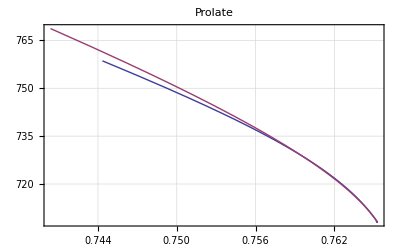
-Graphics-Condensation Fraction αEnergy U^*

```mathematica
labelPlot[
ListLinePlot[
{Table[With[{α=αProlate[e,10^-3,600]},
{α,prolateUStar[0.6*1000(1-α),e,10]}],{e,0.01,0.95,0.01}],
Table[With[{α=αProlateEqui[e,10^-3,600]},
{α,equiProlateUstar[0.6*1000(1-α),e,10]}],{e,0.01,0.95,0.01}]},
PlotLabel->myStyle@"Prolate",PlotRange->All,PlotStyle->Thick,FrameTicksStyle->Directive[Black,16]],
{"Condensation Fraction α","Energy U^*"}]
```

```mathematica
(* Compute the reduced potential after condensation: *)
prolateUStarPostCond[Q_,e_,R0_,η_]:=prolateUStar[Q(1-αProlate[e,η,Q]),e,R0]

(* Compute the total free energy of the system: *)
ℱProlate[e_,η_,Q_]:=Block[{α=αProlate[e,η,Q],b=gcLengthProlate[Q, e, prolateCFixedV[e,10]],𝒜=prolateArea[e,prolateCFixedV[e,10]],Ω=(4/3)π 10^3,Vws=Ω/η,Λ=hPlanck/(3.8027233477250085*10^-23*569.722)},

prolateUStarPostCond[Q,e,10,η]+α(Q Log[(α Q Λ^3)/(𝒜*b)]-Q)+(1-α)(Q Log[((1-α)Q Λ^3)/(Vws-Ω)]-Q)]
```

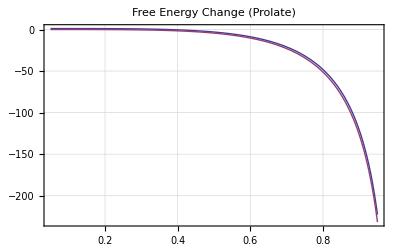
-Graphics-edℱ

```mathematica
(* Plotting the Δℱ at (η = 10^-4): *)
With[{η=10^-2},
labelPlot[Plot[{ℱProlate[e,η,600]-ℱSphere[η,600],ℱProlateEqui[e,η,600]-ℱSphere[η,600]},{e,0.05,0.95},PlotRange->All,PlotLabel->myStyle@"Free Energy Change (Prolate)",PlotStyle->Thick,PlotLegends->None],{"e","dℱ"}]]
```

## Combined

```mathematica
(* The (ES-only) free energy difference between the shape and the reference sphere: *)
ℱShapeDiff[λ_,η_,Q_]:=Which[
λ≤1,ℱOblate[√(1-λ^2),η,Q]-ℱSphere[η,Q],
λ>1,ℱProlate[(√(λ^2-1))/λ,η,Q]-ℱSphere[η,Q]]
```

```mathematica
(* The net shape free energy (with surface tension, numerical coefficient = 1 (dyn/cm) in ((Subscript[k, B] T)/nm^2)) {aspect ratio, packing fraction, tension coefficient, vertex charge, number of vertices}: *)
netℱShapeDiff[λ_,η_, σ_,Q_]:=(ℱShapeDiff[λ,η,Q]+0.24305278499015862*σ*shapeArea[λ])-0.24305278499015862*σ*shapeArea[1]
```

## Controls (reproducing a Figure from Jadhao PRE)

### Controls (Comparison to VJ’s previous work)

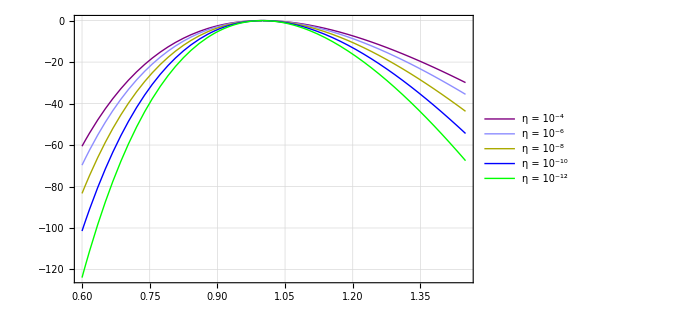
-Graphics-Aspect Ratio λdℱ

```mathematica
(* The inset to Figure 7 of the PRE: *)
labelPlot[Plot[Evaluate@Table[ℱShapeDiff[λ,η,600],{η,{10^-4,10^-6,10^-8,10^-10,10^-12}}],{λ,0.6,1.45},PlotRange->All,PlotStyle->{{Thick,Purple},{Thick,Lighter@Lighter@Blue},{Thick,Darker@Yellow},{Thick,Blue},{Thick,Green}},FrameTicksStyle->Directive[Black,16,FontFamily->"Times New Roman"],PlotLegends->{myStyle/@{"η = 10^-4","η = 10^-6","η = 10^-8","η = 10^-10","η = 10^-12"}},ImageSize->500],{"Aspect Ratio λ","dℱ"}]
```